# GABE NOTEBOOK : Masses

Chris Shepherd, July 2020, christopher.shepherd-3@postgrad.manchester.ac.uk

Clear all variables to avoid naming conflicts.

```mathematica
ClearAll["Global`*"]
globalThickness=0.005
globalFontSize=16;
globalFont="Latin Modern Mono Prop 10";
SetOptions[{ListPlot, ListLogPlot, Plot, LogPlot,ListLogLinearPlot,ListLogLogPlot,RegionPlot},LabelStyle->{ FontFamily->globalFont,FontSize-> globalFontSize, FontColor-> Black }, PlotStyle-> {Black, Thickness-> globalThickness}];

dirlabel=(*"106_64_1000_125";*)"17445_64_1000_125";
plotlabel=(*"106"*)"17445";
```

## PARAMETERS: Set parameters for where to read data and what to plot

The number of labels should be at least as large as the number of fields. Additional labels will be ignored.

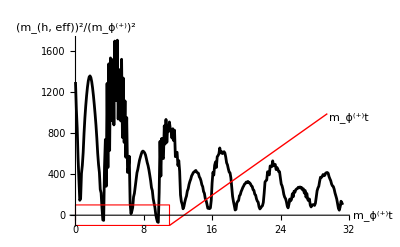

mhplot_17445.pdf

```mathematica
dir="C:\\Users\\admin\\Documents\\PhD_work\\GABE\\local_results_"<>dirlabel<>"\\slices\\";

intablemass=ReadList[dir<>"mass_vs_time.dat", Table[Real,{2}]];
numtimesmass = Length[intablemass]-1;

masstable=Union[Table[{intablemass⟦i,1⟧,intablemass⟦i,2⟧},{i,1,(*numtimesmass*)Round[100*Pi]}]];
(*xmin=0;
xmax=11;
ymin=-100;
ymax=100;

xin0=21; (*centre of inset*)
yin0=1300;*)

massPlot=ListPlot[masstable, Joined-> True, AxesLabel->{"m_ϕ^(+)t", "(m_(h, eff))^2/(m_ϕ^(+))^2"}, PlotRange->{{0,10*Pi},All},
(*Epilog->{ Inset[ 
		ListPlot[masstable, Joined-> True, 
		PlotRange->{{xmin, xmax}, {ymin, ymax}},
		Frame->True,
		FrameStyle->Red,
		FrameTicksStyle->Black,
		ImageSize->150,
		PlotRangeClipping->True
			],
		 {xin0,yin0}],
		Style[Text["m_ϕ^(+)t", {xin0+1*xmax,950}],FontFamily->globalFont, globalFontSize],
		Style[Text["(m_(h, eff))^2/(m_ϕ^(+))^2", {16.5, 2000}],FontFamily->globalFont, globalFontSize],
		Red,Line[{{xmax,ymin}, {xin0+.77xmax,990}}],
		EdgeForm[Red],Transparent,Rectangle[{xmin,ymin}, {xmax, ymax}]
		
		},*)
		PlotRangeClipping->False
]



(*SetDirectory["C:\\Users\\admin\\Desktop\\paper\\figures"];
Export["mhplot_"<>plotlabel<>".pdf", massPlot]*)
```